```mathematica
sampleData = StringSplit["AlphaCentauri to Snowdin = 66
AlphaCentauri to Tambi = 28
AlphaCentauri to Faerun = 60
AlphaCentauri to Norrath = 34
AlphaCentauri to Straylight = 34
AlphaCentauri to Tristram = 3
AlphaCentauri to Arbre = 108
Snowdin to Tambi = 22
Snowdin to Faerun = 12
Snowdin to Norrath = 91
Snowdin to Straylight = 121
Snowdin to Tristram = 111
Snowdin to Arbre = 71
Tambi to Faerun = 39
Tambi to Norrath = 113
Tambi to Straylight = 130
Tambi to Tristram = 35
Tambi to Arbre = 40
Faerun to Norrath = 63
Faerun to Straylight = 21
Faerun to Tristram = 57
Faerun to Arbre = 83
Norrath to Straylight = 9
Norrath to Tristram = 50
Norrath to Arbre = 60
Straylight to Tristram = 27
Straylight to Arbre = 81
Tristram to Arbre = 90","\n"]
```

{AlphaCentauri to Snowdin = 66,AlphaCentauri to Tambi = 28,AlphaCentauri to Faerun = 60,AlphaCentauri to Norrath = 34,AlphaCentauri to Straylight = 34,AlphaCentauri to Tristram = 3,AlphaCentauri to Arbre = 108,Snowdin to Tambi = 22,Snowdin to Faerun = 12,Snowdin to Norrath = 91,Snowdin to Straylight = 121,Snowdin to Tristram = 111,Snowdin to Arbre = 71,Tambi to Faerun = 39,Tambi to Norrath = 113,Tambi to Straylight = 130,Tambi to Tristram = 35,Tambi to Arbre = 40,Faerun to Norrath = 63,Faerun to Straylight = 21,Faerun to Tristram = 57,Faerun to Arbre = 83,Norrath to Straylight = 9,Norrath to Tristram = 50,Norrath to Arbre = 60,Straylight to Tristram = 27,Straylight to Arbre = 81,Tristram to Arbre = 90}

```mathematica
lengths=Flatten[StringReplace[sampleData,{a__~~" to "~~b__~~" = "~~c__}->a<->b->c],1,StringExpression]
```

{AlphaCentauri<->Snowdin→66,AlphaCentauri<->Tambi→28,AlphaCentauri<->Faerun→60,AlphaCentauri<->Norrath→34,AlphaCentauri<->Straylight→34,AlphaCentauri<->Tristram→3,AlphaCentauri<->Arbre→108,Snowdin<->Tambi→22,Snowdin<->Faerun→12,Snowdin<->Norrath→91,Snowdin<->Straylight→121,Snowdin<->Tristram→111,Snowdin<->Arbre→71,Tambi<->Faerun→39,Tambi<->Norrath→113,Tambi<->Straylight→130,Tambi<->Tristram→35,Tambi<->Arbre→40,Faerun<->Norrath→63,Faerun<->Straylight→21,Faerun<->Tristram→57,Faerun<->Arbre→83,Norrath<->Straylight→9,Norrath<->Tristram→50,Norrath<->Arbre→60,Straylight<->Tristram→27,Straylight<->Arbre→81,Tristram<->Arbre→90}

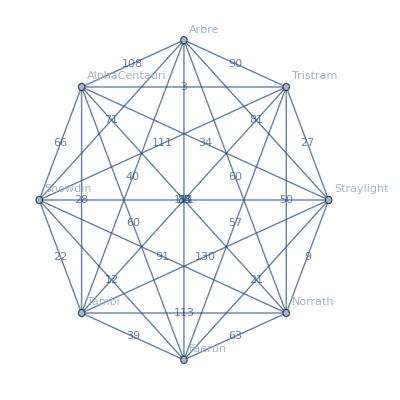

```mathematica
g=Graph[lengths⟦All,1⟧,{EdgeLabels->{"EdgeWeight"},EdgeWeight->ToExpression/@lengths⟦All,2⟧,VertexLabels->"Name"}]
```

```mathematica
Table[FindShortestTour[g,i[[1]],i[[2]]],{i,lengths[[All,1]]}]//TableForm
```

180 | AlphaCentauri
Tristram
Tambi
Arbre
Norrath
Straylight
Faerun
Snowdin
206 | AlphaCentauri
Tristram
Norrath
Straylight
Faerun
Snowdin
Arbre
Tambi
173 | AlphaCentauri
Tristram
Straylight
Norrath
Arbre
Tambi
Snowdin
Faerun
185 | AlphaCentauri
Tristram
Straylight
Faerun
Snowdin
Tambi
Arbre
Norrath
203 | AlphaCentauri
Tristram
Faerun
Snowdin
Tambi
Arbre
Norrath
Straylight
216 | AlphaCentauri
Norrath
Arbre
Tambi
Snowdin
Faerun
Straylight
Tristram
157 | AlphaCentauri
Tristram
Norrath
Straylight
Faerun
Snowdin
Tambi
Arbre
197 | Snowdin
Faerun
Straylight
Tristram
AlphaCentauri
Norrath
Arbre
Tambi
207 | Snowdin
Tambi
Arbre
Norrath
AlphaCentauri
Tristram
Straylight
Faerun
191 | Snowdin
Faerun
Straylight
Tristram
AlphaCentauri
Tambi
Arbre
Norrath
209 | Snowdin
Faerun
Tristram
AlphaCentauri
Tambi
Arbre
Norrath
Straylight
173 | Snowdin
Faerun
Straylight
Norrath
Arbre
Tambi
AlphaCentauri
Tristram
154 | Snowdin
Faerun
Straylight
Norrath
AlphaCentauri
Tristram
Tambi
Arbre
210 | Tambi
AlphaCentauri
Tristram
Straylight
Norrath
Arbre
Snowdin
Faerun
208 | Tambi
Arbre
Snowdin
Faerun
Straylight
Tristram
AlphaCentauri
Norrath
226 | Tambi
Arbre
Snowdin
Faerun
Tristram
AlphaCentauri
Norrath
Straylight
190 | Tambi
Arbre
Snowdin
Faerun
Straylight
Norrath
AlphaCentauri
Tristram
179 | Tambi
Snowdin
Faerun
Straylight
Tristram
AlphaCentauri
Norrath
Arbre
190 | Faerun
Snowdin
Arbre
Tambi
AlphaCentauri
Tristram
Straylight
Norrath
198 | Faerun
Snowdin
Tambi
Arbre
Norrath
AlphaCentauri
Tristram
Straylight
180 | Faerun
Snowdin
Tambi
Arbre
Norrath
Straylight
AlphaCentauri
Tristram
161 | Faerun
Snowdin
Tambi
AlphaCentauri
Tristram
Straylight
Norrath
Arbre
216 | Norrath
AlphaCentauri
Tristram
Tambi
Arbre
Snowdin
Faerun
Straylight
184 | Norrath
Straylight
Faerun
Snowdin
Arbre
Tambi
AlphaCentauri
Tristram
159 | Norrath
AlphaCentauri
Tristram
Straylight
Faerun
Snowdin
Tambi
Arbre
192 | Straylight
Faerun
Snowdin
Tambi
Arbre
Norrath
AlphaCentauri
Tristram
177 | Straylight
Norrath
AlphaCentauri
Tristram
Faerun
Snowdin
Tambi
Arbre
141 | Tristram
AlphaCentauri
Norrath
Straylight
Faerun
Snowdin
Tambi
Arbre

```mathematica
Mod[x,2]
```

Mod[x,2]

```mathematica
x≡2mod 256
```